```mathematica
Solve[{ω==((c^2 k^2)/a^2+α^2)^(1/2),c==(α/ρh)^(1/2)},{c,α}]/.ω->(2 π 14*10^6)/.ρh->23.8*10^-6/.k->2.4048/.a->2.5*10^-6
```

{{c→0.+4.04168×10^10 ⅈ,α→-3.88777×10^16},{c→0.,α→0.}}

```mathematica
Solve[{ω==((c^2 k^2)/a^2)^(1/2)},{c}]/.ω->(2 π 14*10^6)/.ρh->23.8*10^-6/.k->2.4048/.a->2.5*10^-6
```

{{c→-91.4469},{c→91.4469}}

```mathematica
D[c^2/(π a^2)BesselJ[0,(k ρ)/a]BesselJ[0,(k r)/a] Sin[(t-τ) ω]/(BesselJ[1,k]^2 ω),t]
```

(c^2 BesselJ[0,(k r)/a] BesselJ[0,(k ρ)/a] Cos[(t-τ) ω])/(a^2 π BesselJ[1,k]^2)

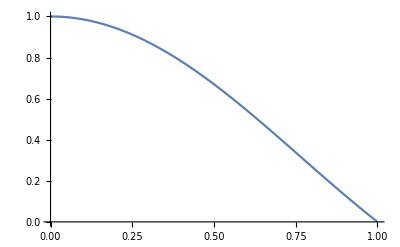

```mathematica
Plot[BesselJ[0,(k ρ)/1]/.k->2.4048,{ρ,0,1}]
```

```mathematica
800 m c^2/(a^2 π BesselJ[1,k]^2)/.c->91/.k->2.4048/.a->2.5*10^-6/.m->4*10^-26
```

5.0074×10^-8

```mathematica
TrigExpand[p((c^2 BesselJ[0,(k r)/a] BesselJ[0,(k ρ)/a] Cos[t ω-τ ω])/(a^2 π BesselJ[1,k]^2))]
```

(c^2 p BesselJ[0,(k r)/a] BesselJ[0,(k ρ)/a] Cos[t ω] Cos[τ ω])/(a^2 π BesselJ[1,k]^2)+(c^2 p BesselJ[0,(k r)/a] BesselJ[0,(k ρ)/a] Sin[t ω] Sin[τ ω])/(a^2 π BesselJ[1,k]^2)

```mathematica
(c^2 /(a^2 π BesselJ[1,k]^2)) BesselJ[0,(k r)/a]( A Cos[t ω]+ B Sin[t ω])
```

```mathematica
b=p BesselJ[0,(k ρ)/a]  Sin[τ ω]
a=p BesselJ[0,(k ρ)/a]  Cos[τ ω]
```

```mathematica
AA=p BesselJ[0,(k ρ)/a]  Sin[τ ω]/.τ->t/.t->3.7413741061162307*10^-11/.ρ->2.3246177976035758*10^-5/.a->2.5*10^-4/.k->2.4047999382019043/.ω->14*10^6 2π/.p->2.4575750639108*10^-19
BB=p BesselJ[0,(k ρ)/a]  Cos[τ ω]/.τ->t/.t->3.7413741061162307*10^-11/.ρ->2.3246177976035758*10^-5/.a->2.5*10^-4/.k->2.4047999382019043/.ω->14*10^6 2π/.p->2.4575750639108*10^-19

(c^2 /(a^2 π BesselJ[1,k]^2)) BesselJ[0,(k r)/a]( B Cos[t ω]+ A Sin[t ω])/.t->3.7413741061162307*10^-11/.ρ->2.3246177976035758*10^-5/.a->2.5*10^-4/.k->2.404799/.ω->14*10^6 2π/.p->2.4575750*10^-19/.r->0/.c->9144/.A->AA/.B->BB
```

7.98728×10^-22

2.42694×10^-19

0.000383453

```mathematica
(c^2 /(a^2 π BesselJ[1,k]^2))BesselJ[0,(k r)/a]/.t->3.7413741061162307*10^-11/.ρ->6.1746459607246375*10^-6/.a->2.5*10^-4/.k->2.404799/.ω->14*10^6 2π/.p->2.4575750*10^-19/.r->0/.c->9144
```

1.57998×10^15

```mathematica
1579980000000000.0
```

1.57998×10^15

```mathematica
BesselJ[0,(k ρ)/a]/.ρ->6.1746459607246375*10^-6/.a->2.5*10^-4/.k->2.4047999382019043
```

0.999118

```mathematica
1579980584116212.0
```

1.57998×10^15

```mathematica
14.0*10^6 2π
```

8.79646×10^7

```mathematica
87964596.748
```

8.79646×10^7

```mathematica
n=1.2276225481611264*^18;
19.7832885629*10^6*2π;
(1000(n (k) T/.k->1.38064852*10^-16/.T->295/.m->4*10^-23)/100000)/10
```

50.

```mathematica
λ=1/(n d^2 π 2^(1/2))/.d->3.3437749430380133*10^-8
```

0.000163982

```mathematica
(4*10^-5)/λ
```

0.243929

```mathematica
5*10^-4/(4.0*10^-5)
```

12.5

```mathematica
4*12.5
```

50.

```mathematica
8*12
```

```mathematica
Solve[((1000(nn (k) T/.k->1.38064852*10^-16/.T->295/.m->4*10^-23)/100000)/10)==50,nn]
```

{{nn→1.22762×10^18}}

```mathematica
(λ /41000)/10
```

3.99956×10^-10

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/drladiges/projects/FHDeX/exec/DSMC

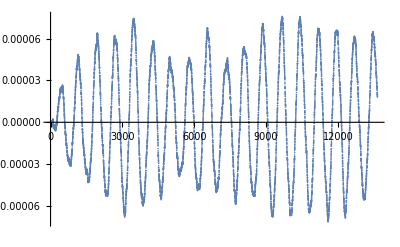

```mathematica
test=Import["out.csv"][[All,1]];
ListPlot[test]
```

```mathematica
test
```

{3.40841×10^-6,6.81412×10^-6,0.0000102202,0.0000136403,0.0000170479,0.0000204494,0.0000238591,0.0000272699,0.0000306835,0.0000340893,0.0000374813,0.0000408795,0.0000442736,0.0000476694,0.0000510615,0.0000544434,0.0000578214,0.0000612032,0.0000645715,0.0000679525,0.0000713107,0.0000746712,0.0000780226,0.0000813942,0.0000847405,0.0000880693,0.0000913944,0.0000947391,0.0000980591,0.000101378,0.000104697,0.000108,0.000111302,0.000114611,0.000117907,0.000121182,0.000124466,0.000127742,0.000130999,0.000134252,0.000137504,0.000140751,0.000143978,0.000147193,0.000150411,0.00015362,0.00015682,0.000160003,0.000163178,0.000166342,0.000169498,0.000172644,0.000175784,0.000178919,0.000182039,0.000185154,0.000188242,0.000191315,0.000194384,0.000197461,0.000200505,0.000203544,0.000206542,0.000209546,0.000212537,0.000215525,0.000218493,0.000221454,0.000224399,0.000227331,0.000230253,0.00023316,0.00023606,0.000238942,0.000241813,0.000244668,0.000247487,0.000250316,0.000253126,0.000255913,0.000258683,0.000261439,0.000264182,0.000266914,0.000269609,0.000272294,0.000274963,0.000277634,0.00028027,0.000282905,0.000285516,0.000288076,0.00029066,0.000293203,0.000295748,0.00029827,0.000300757,0.000303242,0.000305705,0.000308164}

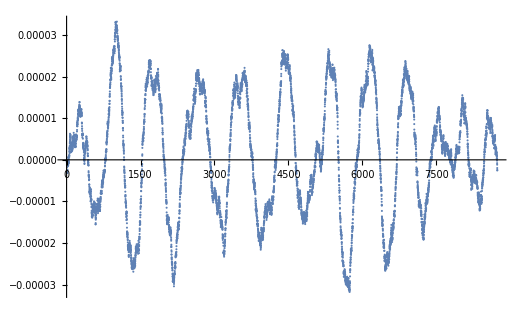
```mathematica
(*12.5*)
-Graphics-
```

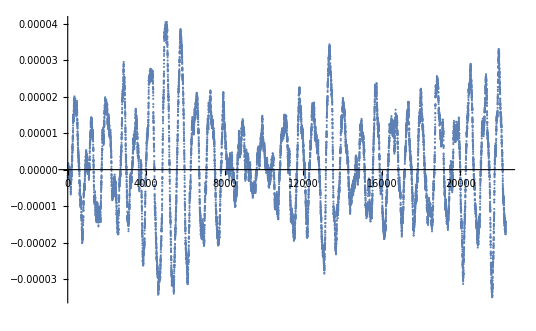
```mathematica
(*13.0*)
-Graphics-
```

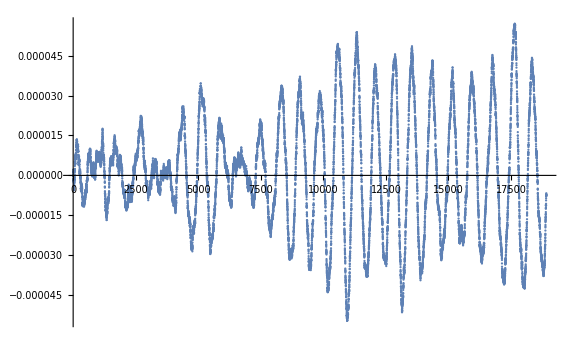
```mathematica
(*12.7*)
-Graphics-
```